```mathematica
DSolve[y'[x]==g ρ,y[x],x]
```

{{y[x]→g x ρ+C[1]}}

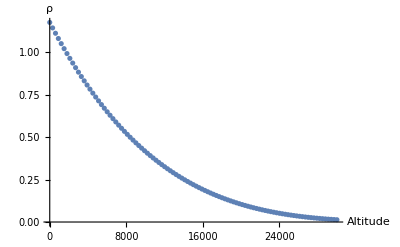

```mathematica
in = Flatten@Import["~/phd-stuff/courses/comp_phys/assignment_7/densities.dat"];
in=Reverse@in;
ListPlot[in,DataRange->{0,30000},AxesLabel->{"Altitude","ρ"}]
```

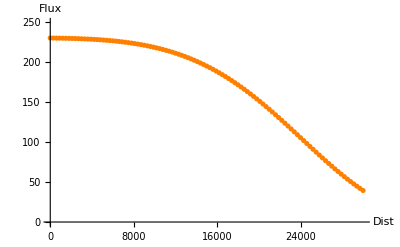

39.4596

```mathematica
in = Flatten@Import["~/phd-stuff/courses/comp_phys/assignment_7/visflux.dat"];
c=ListPlot[in,DataRange->{0,30000},PlotRange->{{0,30000},{0,250}},PlotStyle->Orange,AxesLabel->{"Dist","Flux"}]
in[[Length@in]]
```

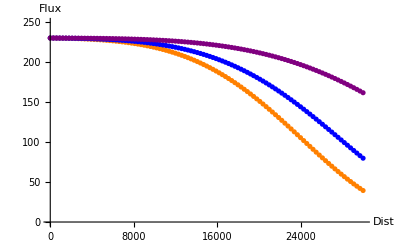

```mathematica
Show[c,a,b]
```

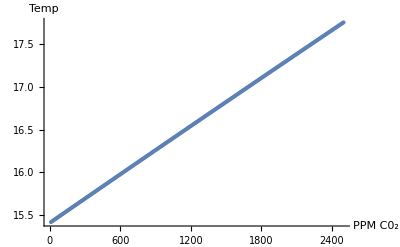

```mathematica
in = Flatten@Import["~/phd-stuff/courses/comp_phys/assignment_7/temps.dat"];
c=ListPlot[in,AxesLabel->{"PPM C0_2","Temp"},DataRange->{10,2500}]
```

6.62607×10^-34

1.38065×10^-23

299792458

300

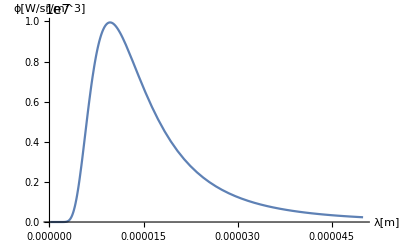

```mathematica
h=6.626070040*^-34
kB=1.38064852*^-23
c=299792458
T=300
Plot[2h c^2/λ^5*1/(Exp[h c/(λ kB T)]-1),{λ,0,50*^-6},PlotRange->All,AxesLabel->{"λ[m]","ϕ[W/sr/m^3]"}]
```